# Finding Most Independent Classifier Trios on Unlabeled Data

The core theorem of this submission shows that if we had error independent classifiers on a sample, we could efficiently calculate the two possible point solutions to their performance and the true prevalence of the two classes. But how can we know the classifiers are actually independent on unlabeled data? This seems like a chicken and egg problem, and it is for evaluation methods that rely on real numbers&mdash;like all probability distribution approaches. In this notebook you will see how we can actually measure distances between the solutions of the purported independent solution and a universal surface that must contain the correct evaluations. This makes algebraic evaluators self-checking on their assumptions.
The notebook is organized as follows:

1. Alarms: we briefly talk about how all alarms have flaws. Proper safety engineering requires that they be evaluated in their application context.
2. A Universal Evaluation Surface Containing the True Performance: Even when we avoid the problem of computing the actual error correlations, we can derive a universal surface of dimension n+1 embedded in the 2n+1 space defined by their label accuracies and prevalence. We test whether the ground truth values for the classifiers do lie on this surface for various trials, and if not, measure their nearest distance to it.
3. Search for Most Independent Trios: We can exploit the distance from the universal evaluation surface to rank trios evaluated on unlabeled data. Using this approach, a search over possible trios is carried out. The results of the search yield a handful of trios with very low error correlations (~2%) on the unlabeled samples.

## Alarms will fail, good engineers know when

There is no perfect alarm. There cannot be one. No one will ever submit to competitions like Stanford HAI’s AI Audit Challenge the perfect tool to carry out its intended auditing task. Good safety engineering requires that we understand the failure properties of any proposed alarm.
  We take it as a given that the only safe AI systems of the future will be based on the use of ensemble methods in one way or another. Our independent trio evaluator is one such ensemble technique that can contribute to that future safety. But it fails. This notebook is about using its failures to find the most independent trios on a particular dataset.
  This is an exercise that cannot be carried out with probabilistic evaluators of noisy judges. By construction they will always return sensible answers&mdash;always real numbers. They never fail! We think that is a flaw for AI safety.

#### Algebraic numbers make AI alarms possible

There are three failure modes for the independent algebraic evaluator that alert us to the inapplicability of its assumptions to a given evaluation context.

Given enough items on a sample test, independent classifiers should produce all possible voting patterns. For three classifiers that means that we should see eight voting patterns during binary classification. If any one of these patterns is absent, we know that the classifiers cannot possibly be independent on the sample. Mathematically this is expressed by the algebraic solver returning the empty set for the Groebner basis of the independent system.

When evaluating classifiers, we know that all possible solutions must be real integer ratios that lie between 0 and 1. Any value for the ensemble that lies outside this range is also a sign that the assumption of error independence must be wrong.

Finally, the independent algebraic evaluator can return complex numbers: a clearly nonsensical answer.

## Initial look at the code and confirming it works

### Getting the dataset and preparing it for training and testing

Mathematica has powerful built-in functions to help us retrieve public datasets. Public datasets are an important part of the scientific/research/development eco-systems. They help promote transparency and reproducibility of research claims.The running example used throughout this submission is the UCI Adult Dataset. There are various reasons this dataset was chosen:

It is public.

It is used to train and test binary classifiers.

It is used in the AI fairness research literature since it contains two sensitive attributes of concern to society - gender and age.

Mathematica curates an extensive data repository. Perhaps we can find UCI Adult in it.

```mathematica
ResourceSearch["UCI"]
```

```mathematica
ResourceSearch["Adult"]
```

The UPenn Dataset Repository is one place we can find the UCI Adult dataset and other ones like it. Let’s use that.

```mathematica
{tsvHeader, benchmarkData} = ImportPennMLBenchmarksDataset["adult"];
```

```mathematica
tsvHeader
```

{age,workclass,fnlwgt,education,education-num,marital-status,occupation,relationship,race,sex,capital-gain,capital-loss,hours-per-week,native-country,target}

### Choosing features for the ensemble of classifiers.

If we could always have classifiers independent on their testing sample errors, then AI safety would be easy to solve by the theorem in TheCoreConcept.nb. The practical reality is that error correlated classifiers are a reality and should be planned for in any evaluator that claims to successfully monitor them.
The engineering approach taken in this notebook is that we can increase their error independence by training them on different features of the data.

### Preparing the benchmark data for training and tests

We first choose a global pool of training and testing separation. In the experiments we are about to make, we want a clear demarcation between the data used for training runs from those used for testing runs. Our tests
are going to involve repeated random draws for training and testing. The training side represents the labeled data we have for building classifiers “in the lab”, if you will. The testing side represents the reality during deployment where we must evaluate without knowledge of the labels. Any mixing of the two pools&mdash;training and testing&mdash;would invalidate any strong conclusions about being able to perform a task without ground truth since the mixing allowed during the experiment would be absent. We have to treat the unlabeled data as it is future data and completely unavailable for the training phases of our experiments.

```mathematica
trainingPoolSize=9000
globalTrainTestSplit=Association[
0->(RandomSample[benchmarkData[0]]//
{Take[#,trainingPoolSize],Drop[#,trainingPoolSize]}&),
1->(RandomSample[benchmarkData[1]]//
{Take[#,trainingPoolSize],Drop[#,trainingPoolSize]}&)];
```

9000

Let’s check our data sizes came out correctly.

```mathematica
Map[Length,globalTrainTestSplit,{2}]
```

<|0→{9000,2687},1→{9000,28155}|>

Looks good. We begin looking at the 7 dimensional space defined by the prevalence and the two label accuracies for each of three classifiers.

## An implicit region that always contains the ground truth point

The math of the central theorem is agnostic as to its meaning. Application context determines that meaning. We are using that math to estimate performance statistics for the classifiers and one environmental variable&mdash; the prevalence. These statistics are, by definition, confined to the range of 0 to 1. In addition, we know that the their true values must be some ratio of integers. Our uncertainty is thus bound by a unit hypercube anchored at the origin and with the diagonally opposite point at the (1,1,1,1,1,1,1) point.
This section now considers using the decisions of the classifiers to shrink that unit cube uncertainty to a surface of dimension 4 in the 7 dimensional space. We will build that surface and then train a trio of classifiers. We then confirm if their performance lies on the implicit region as claimed.

### Doing a run and testing surface membership

```mathematica
Clear[FirstSolutionPoint]
FirstSolutionPoint[eval_List]:=Last@eval//First//First//Association
Clear[SecondSolutionPoint]
SecondSolutionPoint[eval_List]:=Last@eval//First//Last//Association
```

```mathematica
Clear[GroundTruthCoordinates]
GroundTruthCoordinates[point_Association]:={Subscript[P, α],Subscript[P, 1,α],Subscript[P, 1,β],Subscript[P, 2,α],Subscript[P, 2,β],Subscript[P, 3,α],Subscript[P, 3,β]}/.point
```

```mathematica
Clear[SelectTrainTestSplit]
SelectTrainTestSplit[data_,nTestAlpha_Integer,nTrain_Integer]:=
Association[
0->{
RandomSample[First@data[0]]//Take[#,nTrain]&,
RandomSample[Last@data[0]]//Take[#,nTestAlpha]&},
1->{
RandomSample[First@data[1]]//Take[#,nTrain]&,
RandomSample[Last@data[1]]//Take[#,2*nTestAlpha//Floor]&}]
```

```mathematica
Clear[IsNotComplexQ]
IsNotComplexQ[eval_List]:=eval//Last//Flatten//Last/@#&//Not@MemberQ[#,_Complex,Infinity]&
```

```mathematica
(* We do a random partition of the UCI Adult features *)
classifiersFeatures=uciAdultFeatures[[Complement[Range@14,{1,10}]]]//
RandomSample//
Partition[#,3]&//
Take[#,3]&//
Map[Sort,#]&//Sort;
(* Settings for training and testing sample sizes *)
nTestAlpha=2000;
nTrain=3600;
nClassifiers=3;

classifierTypes = Table["NaiveBayes",{3}];
runTrainTestSplit=SelectTrainTestSplit[globalTrainTestSplit,nTestAlpha,nTrain];
trainingIndices=Transpose@{
RandomSample[Range@nTrain]//Partition[#,Floor[nTrain/nClassifiers]]&//Take[#,nClassifiers]&,
RandomSample[Range@nTrain]//Partition[#,Floor[nTrain/nClassifiers]]&//Take[#,nClassifiers]&};
classifiersData=Table[Map[#[[First@Transpose@features]]&,runTrainTestSplit,{3}],{features,classifiersFeatures}];

classifiers = TrainClassifiersDisjoint[classifiersData,classifierTypes,trainingIndices,Map[(Last@Transpose@#)&,classifiersFeatures]];

eval=AlgebraicallyEvaluateClassifiers[classifiers,classifiersData];

(* Now display the 1st solution on the left, the true solution in the center,
and the 2nd solution on the right *)
If[IsNotComplexQ[eval],
tp1=FirstSolutionPoint[eval];
tp2=SecondSolutionPoint[eval];
vcbl=LabelCounts[classifiers,classifiersData];
reg=GroundTruthImplicitRegion[vcbl,Range@3,α];
points=Map[{GroundTruthCoordinates@#//N,RegionNearest[reg,GroundTruthCoordinates@#//N]}&,{tp1,tp2}];
Print[
(* Comparison between true performance and the estimates *)points//Transpose/@#&//Flatten[#,1]&//Partition[#,7]&//Join[Take[#,1],{{Subscript[P, α],Subscript[P, 1,α],Subscript[P, 1,β],Subscript[P, 2,α],Subscript[P, 2,β],Subscript[P, 3,α],Subscript[P, 3,β]}},{{Subscript[P, α],Subscript[P, 1,α],Subscript[P, 1,β],Subscript[P, 2,α],Subscript[P, 2,β],Subscript[P, 3,α],Subscript[P, 3,β]}/.(eval//First)//N},Take[#,-1]]&//Transpose//Flatten/@#&//Grid[#,Dividers->All]&];
(* The distances of the two independent solutions from the universal surface *)
points//Map[(First@#-Last@#)&,#]&//Map[#^2&,#,{2}]&//Total/@#&//Sqrt/@#&,
Nothing]
```

0.482217 | 0.482217 | P_α | 0.333333 | 0.517783 | 0.517783
0.359554 | 0.359554 | P_(1,α) | 0.543 | 0.530693 | 0.530693
0.469307 | 0.469307 | P_(1,β) | 0.59925 | 0.640446 | 0.640446
0.101356 | 0.101356 | P_(2,α) | 0.8945 | 0.898621 | 0.898621
0.101379 | 0.101379 | P_(2,β) | 0.676 | 0.898644 | 0.898644
0.0598414 | 0.0598414 | P_(3,α) | 0.8615 | 0.915718 | 0.915718
0.0842822 | 0.0842822 | P_(3,β) | 0.67625 | 0.940159 | 0.940159

{9.82105×10^-8,6.70706×10^-8}

Notice how the independent solutions for this randomly chosen partition are close to the universal surface. Let’s do another run.

```mathematica
(* We do a random partition of the UCI Adult features *)
classifiersFeatures=uciAdultFeatures[[Complement[Range@14,{1,10}]]]//
RandomSample//
Partition[#,3]&//
Take[#,3]&//
Map[Sort,#]&//Sort;
(* Settings for training and testing sample sizes *)
nTestAlpha=2000;
nTrain=3600;
nClassifiers=3;

classifierTypes = Table["NaiveBayes",{3}];
runTrainTestSplit=SelectTrainTestSplit[globalTrainTestSplit,nTestAlpha,nTrain];
trainingIndices=Transpose@{
RandomSample[Range@nTrain]//Partition[#,Floor[nTrain/nClassifiers]]&//Take[#,nClassifiers]&,
RandomSample[Range@nTrain]//Partition[#,Floor[nTrain/nClassifiers]]&//Take[#,nClassifiers]&};
classifiersData=Table[Map[#[[First@Transpose@features]]&,runTrainTestSplit,{3}],{features,classifiersFeatures}];

classifiers = TrainClassifiersDisjoint[classifiersData,classifierTypes,trainingIndices,Map[(Last@Transpose@#)&,classifiersFeatures]];

eval=AlgebraicallyEvaluateClassifiers[classifiers,classifiersData];

(* Now display the 1st solution on the left, the true solution in the center,
and the 2nd solution on the right *)
If[IsNotComplexQ[eval],
tp1=FirstSolutionPoint[eval];
tp2=SecondSolutionPoint[eval];
vcbl=LabelCounts[classifiers,classifiersData];
reg=GroundTruthImplicitRegion[vcbl,Range@3,α];
points=Map[{GroundTruthCoordinates@#//N,RegionNearest[reg,GroundTruthCoordinates@#//N]}&,{tp1,tp2}];
Print[
(* Comparison between true performance and the estimates *)points//Transpose/@#&//Flatten[#,1]&//Partition[#,7]&//Join[Take[#,1],{{Subscript[P, α],Subscript[P, 1,α],Subscript[P, 1,β],Subscript[P, 2,α],Subscript[P, 2,β],Subscript[P, 3,α],Subscript[P, 3,β]}},{{Subscript[P, α],Subscript[P, 1,α],Subscript[P, 1,β],Subscript[P, 2,α],Subscript[P, 2,β],Subscript[P, 3,α],Subscript[P, 3,β]}/.(eval//First)//N},Take[#,-1]]&//Transpose//Flatten/@#&//Grid[#,Dividers->All]&];
(* The distances of the two independent solutions from the universal surface *)
points//Map[(First@#-Last@#)&,#]&//Map[#^2&,#,{2}]&//Total/@#&//Sqrt/@#&,
Nothing]
```

0.407942 | 0.465207 | P_α | 0.333333 | 0.592058 | 0.534797
-0.221821 | 0 | P_(1,α) | 0.868 | 1.00495 | 0.943348
-0.00495304 | 0.056644 | P_(1,β) | 0.67725 | 1.22182 | 1.
0.171126 | 0.185453 | P_(2,α) | 0.6095 | 0.441439 | 0.457908
0.558561 | 0.542079 | P_(2,β) | 0.808 | 0.828874 | 0.814536
0.132449 | 0.164893 | P_(3,α) | 0.8265 | 0.744526 | 0.781828
0.255474 | 0.218157 | P_(3,β) | 0.671 | 0.867551 | 0.835096

{0.24331,0.24331}

This is an example of a trio of classifiers that are clearly not error independent on the test sample. Real, out of bounds values are being returned for some of the classifiers.

## Scanning for feature partitions that minimize that distance

We can now test proposed disjoint feature partitions and see how far their independent solution is from the universal surface.

```mathematica
featurePartitions=Table[uciAdultFeatures[[Complement[Range@14,{1,10}]]]//
RandomSample//
Partition[#,3]&//
Take[#,3]&//
Map[Sort,#]&//Sort,{1000}]//DeleteDuplicates;
Length@featurePartitions
```

994

```mathematica
searchDS=globalTrainTestSplit;
nTestAlpha=1000;
nTrain=1800;
nClassifiers=3;
classifierTypes = Table[{"LogisticRegression","L1Regularization"->0.1,"L2Regularization"->0.5,"OptimizationMethod"->"Newton"},{nClassifiers}];
(*classifiersFeatures=featurePartitions[[RandomChoice@stage2Partitions]]; *)
runs=Table[

runTrainTestSplit=SelectTrainTestSplit[searchDS,nTestAlpha,nTrain];
trainingIndices=Transpose@{
RandomSample[Range@nTrain]//Partition[#,Floor[nTrain/nClassifiers]]&//Take[#,nClassifiers]&,
RandomSample[Range@nTrain]//Partition[#,Floor[nTrain/nClassifiers]]&//Take[#,nClassifiers]&};
classifiersData=Table[Map[#[[First@Transpose@features]]&,runTrainTestSplit,{3}],{features,classifiersFeatures}];
classifiers = TrainClassifiersDisjoint[classifiersData,classifierTypes,trainingIndices,Map[(Last@Transpose@#)&,classifiersFeatures]];
vcbl=LabelCounts[classifiers,classifiersData];

eval=AlgebraicallyEvaluateClassifiers[classifiers,classifiersData];
If[IsNotComplexQ[eval],
tp1=FirstSolutionPoint[eval];
tp2=SecondSolutionPoint[eval];
reg=GroundTruthImplicitRegion[vcbl,Range@3,α];
points=Map[{GroundTruthCoordinates@#//N,RegionNearest[reg,GroundTruthCoordinates@#//N]}&,{tp1,tp2}];
points//Map[(First@#-Last@#)&,#]&//Map[#^2&,#,{2}]&//Total/@#&//Sqrt/@#&,
Nothing],
{classifiersFeatures,featurePartitions//RandomSample[#,10]&},{20}];
```

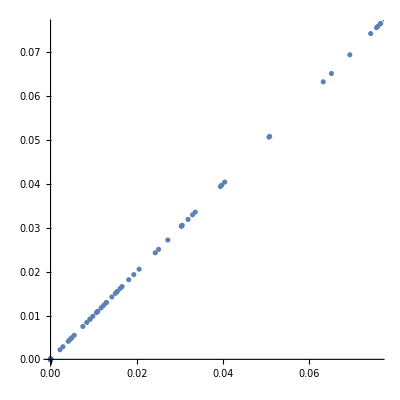

```mathematica
runs//Flatten[#,1]&//ListPlot[#,AspectRatio->1]&
```

```mathematica
Length/@runs
```

{20,20,20,20,20,20,20,20,20,20}

#### Scanning through all the partitions

We want to find the best feature partitions. We have no idea how the partitions are doing on the unlabeled data but we can test how far the independent solution is straying from the ground truth surface. To make the search efficient, we want to eliminate about half our candidates each time. Let’s see how many trials we have to do on this data to discover outright failures.

```mathematica
searchDS=globalTrainTestSplit;
nTestAlpha=2000;
nTrain=3600;
nClassifiers=3;
classifierTypes = Table[{"LogisticRegression","L1Regularization"->0.1,"L2Regularization"->0.5,"OptimizationMethod"->"Newton"},{nClassifiers}];
runs=Table[
vals={};
For[i=0,i<5,i++,
runTrainTestSplit=SelectTrainTestSplit[searchDS,nTestAlpha,nTrain];
trainingIndices=Transpose@{
RandomSample[Range@nTrain]//Partition[#,Floor[nTrain/nClassifiers]]&//Take[#,nClassifiers]&,
RandomSample[Range@nTrain]//Partition[#,Floor[nTrain/nClassifiers]]&//Take[#,nClassifiers]&};
classifiersData=Table[Map[#[[First@Transpose@features]]&,runTrainTestSplit,{3}],{features,classifiersFeatures}];
classifiers = TrainClassifiersDisjoint[classifiersData,classifierTypes,trainingIndices,Map[(Last@Transpose@#)&,classifiersFeatures]];
vcbl=LabelCounts[classifiers,classifiersData];
(* The algebraic evaluation cannot work unless all 8 voting patterns are
observed. Any one of them being absent is a clear signal the classifiers
are too correlated in the sample *)
eval=AlgebraicallyEvaluateClassifiers[classifiers,classifiersData];
If[IsNotComplexQ[eval]&&Not@MatchQ[eval,{_,{{}}}],
tp1=FirstSolutionPoint[eval];
tp2=SecondSolutionPoint[eval];
reg=GroundTruthImplicitRegion[vcbl,Range@3,α];
points=Map[{GroundTruthCoordinates@#//N,RegionNearest[reg,GroundTruthCoordinates@#//N]}&,{tp1,tp2}];
AppendTo[vals,points//Map[(First@#-Last@#)&,#]&//Map[#^2&,#,{2}]&//Total/@#&//Sqrt/@#&],
Break[]]];
vals,
{classifiersFeatures,featurePartitions//Take[#,All]&}];
```

$Aborted

```mathematica
runs//Length/@#&//Counts//KeySort
```

<|0→7,1→5,2→7,3→9,4→5,5→961|>

```mathematica
runs//Select[#,Length@#==5&]&//Flatten/@#&//Min/@#&//MapIndexed[{#2[[1]],#1}&,#]&//Select[#,Last@#<0.000000007&]&
```

{{49,8.80653×10^-10},{54,0.},{70,1.51215×10^-9},{79,5.36251×10^-9},{86,0.},{173,0.},{198,8.01218×10^-10},{258,0.},{363,4.47932×10^-9},{375,5.87618×10^-10},{467,6.81655×10^-9},{589,1.84418×10^-9},{591,2.58868×10^-9},{597,0.},{639,0.},{707,2.94836×10^-9},{771,0.},{776,5.18745×10^-9},{783,6.88984×10^-9},{874,0.},{911,0.}}

```mathematica
featurePartitions[[54]]
```

{{{2,Nominal},{8,Nominal},{13,Numerical}},{{3,Numerical},{9,Nominal},{11,Numerical}},{{5,Nominal},{12,Numerical},{14,Nominal}}}

```mathematica
runs
```

{{{0.02745,0.02745},{0.00370622,0.00370621},{0.00304244,0.00304241}},{{0.0369642,0.0369642},{1.03139×10^-7,1.02443×10^-7},{0.0711846,0.0711846}}}

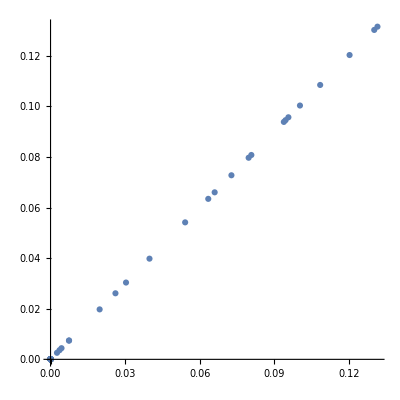

```mathematica
runs//Flatten[#,1]&//ListPlot[#,AspectRatio->1]&
```

```mathematica
featurePartitions[[54]]
```

{{{2,Nominal},{8,Nominal},{13,Numerical}},{{3,Numerical},{9,Nominal},{11,Numerical}},{{5,Nominal},{12,Numerical},{14,Nominal}}}

### Feature partitions that are most error independent when using different algorithms

Now that we have some initial idea of what feature partitions lead to more independent trios, we can increase possible independence by training the partitions using different algorithms. We arbitrarily pick Naive Bayes, Logistic Regression and Random Forest as our three alternative algorithms. We scan the proposed feature partitions and try to identify partitions that are near the universal surface for all three algorithms.

```mathematica
classifiersFeatures=featurePartitions[[258]]
```

{{{2,Nominal},{4,Nominal},{14,Nominal}},{{3,Numerical},{9,Nominal},{11,Numerical}},{{6,Nominal},{8,Nominal},{13,Numerical}}}

```mathematica
(* Testing logistic regression *)
searchDS=globalTrainTestSplit;
nTestAlpha=2000;
nTrain=3600;
nClassifiers=3;
classifierTypes = Table[{"LogisticRegression","L1Regularization"->0.1,"L2Regularization"->0.5,"OptimizationMethod"->"StochasticGradientDescent"},{nClassifiers}];
runsA=Table[
vals={};
For[i=0,i<5,i++,
runTrainTestSplit=SelectTrainTestSplit[globalTrainTestSplit,nTestAlpha,nTrain];
trainingIndices=Transpose@{
RandomSample[Range@nTrain]//Partition[#,Floor[nTrain/nClassifiers]]&//Take[#,nClassifiers]&,
RandomSample[Range@nTrain]//Partition[#,Floor[nTrain/nClassifiers]]&//Take[#,nClassifiers]&};
classifiersData=Table[Map[#[[First@Transpose@features]]&,runTrainTestSplit,{3}],{features,classifiersFeatures}];
classifiers = TrainClassifiersDisjoint[classifiersData,classifierTypes,trainingIndices,Map[(Last@Transpose@#)&,classifiersFeatures]];
vcbl=LabelCounts[classifiers,classifiersData];
(* The algebraic evaluation cannot work unless all 8 voting patterns are
observed. Any one of them being absent is a clear signal the classifiers
are too correlated in the sample *)
eval=AlgebraicallyEvaluateClassifiers[classifiers,classifiersData];
If[IsNotComplexQ[eval]&&Not@MatchQ[eval,{_,{{}}}],
tp1=FirstSolutionPoint[eval];
tp2=SecondSolutionPoint[eval];
reg=GroundTruthImplicitRegion[vcbl,Range@3,α];
points=Map[{GroundTruthCoordinates@#//N,RegionNearest[reg,GroundTruthCoordinates@#//N]}&,{tp1,tp2}];
AppendTo[vals,points//Map[(First@#-Last@#)&,#]&//Map[#^2&,#,{2}]&//Total/@#&//Sqrt/@#&],
Break[]]];
vals,
{classifiersFeatures,featurePartitions//Take[#,All]&}];
```

Let’s pick the feature partitions that were least distant from the universal surface.

```mathematica
runBIndices=runsA//Select[#,Length@#==5&]&//Flatten/@#&//Max/@#&//MapIndexed[{#2[[1]],#1}&,#]&//Select[#,Last@#<0.00000007&]&//First/@#&
```

{31,66,77,85,191,199,258,279,294,297,304,364,367,387,396,412,432,434,438,441,461,491,502,576,597,604,605,627,655,676,702,717,745}

```mathematica
(* Testing Naive Bayes with the partitions selected above *)
nTestAlpha=2000;
nTrain=3600;
nClassifiers=3;
classifierTypes = Table[{"NaiveBayes","SmoothingParameter"->0.3},{nClassifiers}];
runsB=Table[
vals={};
For[i=0,i<5,i++,
runTrainTestSplit=SelectTrainTestSplit[globalTrainTestSplit,nTestAlpha,nTrain];
trainingIndices=Transpose@{
RandomSample[Range@nTrain]//Partition[#,Floor[nTrain/nClassifiers]]&//Take[#,nClassifiers]&,
RandomSample[Range@nTrain]//Partition[#,Floor[nTrain/nClassifiers]]&//Take[#,nClassifiers]&};
classifiersData=Table[Map[#[[First@Transpose@features]]&,runTrainTestSplit,{3}],{features,classifiersFeatures}];
classifiers = TrainClassifiersDisjoint[classifiersData,classifierTypes,trainingIndices,Map[(Last@Transpose@#)&,classifiersFeatures]];
vcbl=LabelCounts[classifiers,classifiersData];
(* The algebraic evaluation cannot work unless all 8 voting patterns are
observed. Any one of them being absent is a clear signal the classifiers
are too correlated in the sample *)
eval=AlgebraicallyEvaluateClassifiers[classifiers,classifiersData];
If[IsNotComplexQ[eval]&&Not@MatchQ[eval,{_,{{}}}],
tp1=FirstSolutionPoint[eval];
tp2=SecondSolutionPoint[eval];
reg=GroundTruthImplicitRegion[vcbl,Range@3,α];
points=Map[{GroundTruthCoordinates@#//N,RegionNearest[reg,GroundTruthCoordinates@#//N]}&,{tp1,tp2}];
AppendTo[vals,points//Map[(First@#-Last@#)&,#]&//Map[#^2&,#,{2}]&//Total/@#&//Sqrt/@#&],
Break[]]];
vals,
{classifiersFeatures,featurePartitions[[runBIndices]]//Take[#,All]&}];
```

```mathematica
runsB
```

{{{7.56382×10^-8,6.75039×10^-8},{7.05933×10^-8,6.98582×10^-8},{7.46558×10^-8,6.89726×10^-8},{7.48531×10^-8,7.10319×10^-8},{8.24557×10^-8,8.03395×10^-8}},{{8.33658×10^-8,8.02548×10^-8},{7.83869×10^-8,7.80456×10^-8},{6.8143×10^-8,6.509×10^-8},{8.30316×10^-8,7.77816×10^-8},{8.34113×10^-8,7.57439×10^-8}}}

```mathematica
(* Test Random Forest trios using the partitions that did best with Logistic Regression *)
nTestAlpha=2000;
nTrain=3600;
nClassifiers=3;
classifierTypes = Table[{"RandomForest","DistributionSmoothing"->0.3,"LeafSize"->100,"TreeNumber"->20},{nClassifiers}];
runsC=Table[
vals={};
For[i=0,i<5,i++,
runTrainTestSplit=SelectTrainTestSplit[globalTrainTestSplit,nTestAlpha,nTrain];
trainingIndices=Transpose@{
RandomSample[Range@nTrain]//Partition[#,Floor[nTrain/nClassifiers]]&//Take[#,nClassifiers]&,
RandomSample[Range@nTrain]//Partition[#,Floor[nTrain/nClassifiers]]&//Take[#,nClassifiers]&};
classifiersData=Table[Map[#[[First@Transpose@features]]&,runTrainTestSplit,{3}],{features,classifiersFeatures}];
classifiers = TrainClassifiersDisjoint[classifiersData,classifierTypes,trainingIndices,Map[(Last@Transpose@#)&,classifiersFeatures]];
vcbl=LabelCounts[classifiers,classifiersData];
(* The algebraic evaluation cannot work unless all 8 voting patterns are
observed. Any one of them being absent is a clear signal the classifiers
are too correlated in the sample *)
eval=AlgebraicallyEvaluateClassifiers[classifiers,classifiersData];
If[IsNotComplexQ[eval]&&Not@MatchQ[eval,{_,{{}}}],
tp1=FirstSolutionPoint[eval];
tp2=SecondSolutionPoint[eval];
reg=GroundTruthImplicitRegion[vcbl,Range@3,α];
points=Map[{GroundTruthCoordinates@#//N,RegionNearest[reg,GroundTruthCoordinates@#//N]}&,{tp1,tp2}];
AppendTo[vals,points//Map[(First@#-Last@#)&,#]&//Map[#^2&,#,{2}]&//Total/@#&//Sqrt/@#&],
Break[]]];
vals,
{classifiersFeatures,featurePartitions[[runBIndices]]//Take[#,All]&}];
```

```mathematica
runsC
```

{{{6.62232×10^-8,6.87912×10^-8},{7.16667×10^-8,7.83271×10^-8},{8.01753×10^-8,8.03323×10^-8},{8.46475×10^-8,8.28071×10^-8},{6.34998×10^-8,7.19226×10^-8}},{{7.49416×10^-8,7.47699×10^-8},{7.29262×10^-8,7.34294×10^-8},{7.63028×10^-8,7.27233×10^-8},{8.18266×10^-8,8.52058×10^-8},{8.18765×10^-8,1.04288×10^-7}}}

```mathematica
indicesB=runsB//Select[#,Length@#==5&]&//Flatten/@#&//Max/@#&//MapIndexed[{#2[[1]],#1}&,#]&//Select[#,Last@#<0.00000008&]&//First/@#&
```

{7,11,18}

```mathematica
indicesC=runsC//Select[#,Length@#==5&]&//Flatten/@#&//Max/@#&//MapIndexed[{#2[[1]],#1}&,#]&//Select[#,Last@#<0.0000001&]&//First/@#&
```

{1,2,5,7,8,9,11,14,18,24,26}

```mathematica
runBIndices[[{7,11,18}]]
```

{258,304,434}

```mathematica
(* How good is partition 258? *)
classifiersFeatures=featurePartitions[[258]]
nTestAlpha=2000;
nTrain=3600;
nClassifiers=3;
classifierTypes={{"RandomForest","DistributionSmoothing"->0.3,"LeafSize"->100,"TreeNumber"->20},
{"NaiveBayes","SmoothingParameter"->0.3},
{"LogisticRegression","L1Regularization"->0.1,"L2Regularization"->0.5,"OptimizationMethod"->"StochasticGradientDescent"}};
runTrainTestSplit=SelectTrainTestSplit[globalTrainTestSplit,nTestAlpha,nTrain];
trainingIndices=Transpose@{
RandomSample[Range@nTrain]//Partition[#,Floor[nTrain/nClassifiers]]&//Take[#,nClassifiers]&,
RandomSample[Range@nTrain]//Partition[#,Floor[nTrain/nClassifiers]]&//Take[#,nClassifiers]&};
classifiersData=Table[Map[#[[First@Transpose@features]]&,runTrainTestSplit,{3}],{features,classifiersFeatures}];
classifiers = TrainClassifiersDisjoint[classifiersData,classifierTypes,trainingIndices,Map[(Last@Transpose@#)&,classifiersFeatures]];
eval=AlgebraicallyEvaluateClassifiers[classifiers,classifiersData];
If[IsNotComplexQ[eval],
tp1=FirstSolutionPoint[eval];
tp2=SecondSolutionPoint[eval];
vcbl=LabelCounts[classifiers,classifiersData];
reg=GroundTruthImplicitRegion[vcbl,Range@3,α];
points=Map[{GroundTruthCoordinates@#//N,RegionNearest[reg,GroundTruthCoordinates@#//N]}&,{tp1,tp2}];
Print[points//Transpose/@#&//Flatten[#,1]&//Partition[#,7]&//Join[Take[#,1],{{Subscript[P, α],Subscript[P, 1,α],Subscript[P, 1,β],Subscript[P, 2,α],Subscript[P, 2,β],Subscript[P, 3,α],Subscript[P, 3,β]}},{{Subscript[P, α],Subscript[P, 1,α],Subscript[P, 1,β],Subscript[P, 2,α],Subscript[P, 2,β],Subscript[P, 3,α],Subscript[P, 3,β]}/.(eval//First)//N},Take[#,-1]]&//Transpose//Flatten/@#&//Grid[#,Dividers->All]&];
points//Map[(First@#-Last@#)&,#]&//Map[#^2&,#,{2}]&//Total/@#&//Sqrt/@#&,
Nothing]
eval//First//N
```

{{{2,Nominal},{4,Nominal},{14,Nominal}},{{3,Numerical},{9,Nominal},{11,Numerical}},{{6,Nominal},{8,Nominal},{13,Numerical}}}

0.305063 | 0.305063 | P_α | 0.333333 | 0.694937 | 0.694937
0.648225 | 0.648225 | P_(1,α) | 0.6475 | 0.315497 | 0.315497
0.684503 | 0.684503 | P_(1,β) | 0.69825 | 0.351775 | 0.351775
0.403756 | 0.403756 | P_(2,α) | 0.374 | 0.211284 | 0.211284
0.788716 | 0.788716 | P_(2,β) | 0.782 | 0.596244 | 0.596244
0.99043 | 0.99043 | P_(3,α) | 0.9105 | 0.45523 | 0.45523
0.54477 | 0.54477 | P_(3,β) | 0.5275 | 0.00956953 | 0.00956952

{8.00191×10^-8,8.16933×10^-8}

<|P_α→0.333333,P_(1,α)→0.6475,P_(2,α)→0.374,P_(3,α)→0.9105,P_(1,β)→0.69825,P_(2,β)→0.782,P_(3,β)→0.5275,Γ_(1,2,α)→0.010835,Γ_(1,3,α)→-0.00754875,Γ_(2,3,α)→-0.001527,Γ_(1,2,β)→-0.0030315,Γ_(1,3,β)→0.00992313,Γ_(2,3,β)→0.010745,Γ_(1,2,3,α)→0.00245547,Γ_(1,2,3,β)→-0.00069508|>

Wow. That is really good.

## Another Train/Test Split

We found a feature partition that did very well given a global train/test split. Is the partition dependent on that particular split? Let’s test another global train/test split.

```mathematica
trainingPoolSize=9000
globalTrainTestSplit=Association[
0->(RandomSample[benchmarkData[0]]//
{Take[#,trainingPoolSize],Drop[#,trainingPoolSize]}&),
1->(RandomSample[benchmarkData[1]]//
{Take[#,trainingPoolSize],Drop[#,trainingPoolSize]}&)];
```

9000

```mathematica
(* How good is partition 258? *)
classifiersFeatures=featurePartitions[[258]]
nTestAlpha=2000;
nTrain=3600;
nClassifiers=3;
classifierTypes={{"RandomForest","DistributionSmoothing"->0.3,"LeafSize"->100,"TreeNumber"->20},
{"NaiveBayes","SmoothingParameter"->0.3},
{"LogisticRegression","L1Regularization"->0.1,"L2Regularization"->0.5,"OptimizationMethod"->"StochasticGradientDescent"}};
runTrainTestSplit=SelectTrainTestSplit[globalTrainTestSplit,nTestAlpha,nTrain];
trainingIndices=Transpose@{
RandomSample[Range@nTrain]//Partition[#,Floor[nTrain/nClassifiers]]&//Take[#,nClassifiers]&,
RandomSample[Range@nTrain]//Partition[#,Floor[nTrain/nClassifiers]]&//Take[#,nClassifiers]&};
classifiersData=Table[Map[#[[First@Transpose@features]]&,runTrainTestSplit,{3}],{features,classifiersFeatures}];
classifiers = TrainClassifiersDisjoint[classifiersData,classifierTypes,trainingIndices,Map[(Last@Transpose@#)&,classifiersFeatures]];
eval=AlgebraicallyEvaluateClassifiers[classifiers,classifiersData];
If[IsNotComplexQ[eval],
tp1=FirstSolutionPoint[eval];
tp2=SecondSolutionPoint[eval];
vcbl=LabelCounts[classifiers,classifiersData];
reg=GroundTruthImplicitRegion[vcbl,Range@3,α];
points=Map[{GroundTruthCoordinates@#//N,RegionNearest[reg,GroundTruthCoordinates@#//N]}&,{tp1,tp2}];
Print[points//Transpose/@#&//Flatten[#,1]&//Partition[#,7]&//Join[Take[#,1],{{Subscript[P, α],Subscript[P, 1,α],Subscript[P, 1,β],Subscript[P, 2,α],Subscript[P, 2,β],Subscript[P, 3,α],Subscript[P, 3,β]}},{{Subscript[P, α],Subscript[P, 1,α],Subscript[P, 1,β],Subscript[P, 2,α],Subscript[P, 2,β],Subscript[P, 3,α],Subscript[P, 3,β]}/.(eval//First)//N},Take[#,-1]]&//Transpose//Flatten/@#&//Grid[#,Dividers->All]&];
points//Map[(First@#-Last@#)&,#]&//Map[#^2&,#,{2}]&//Total/@#&//Sqrt/@#&,
Nothing]
eval//First//N
```

{{{2,Nominal},{4,Nominal},{14,Nominal}},{{3,Numerical},{9,Nominal},{11,Numerical}},{{6,Nominal},{8,Nominal},{13,Numerical}}}

0.472044 | 0.472044 | P_α | 0.333333 | 0.527956 | 0.527956
0.594804 | 0.594804 | P_(1,α) | 0.643 | 0.238138 | 0.238138
0.761862 | 0.761862 | P_(1,β) | 0.71175 | 0.405196 | 0.405196
0.755528 | 0.755528 | P_(2,α) | 0.7515 | 0.561014 | 0.561014
0.438986 | 0.438986 | P_(2,β) | 0.3965 | 0.244472 | 0.244472
0.78863 | 0.78863 | P_(3,α) | 0.899 | 0.456601 | 0.456601
0.543399 | 0.543399 | P_(3,β) | 0.5295 | 0.21137 | 0.21137

{6.29836×10^-8,6.57767×10^-8}

<|P_α→0.333333,P_(1,α)→0.643,P_(2,α)→0.7515,P_(3,α)→0.899,P_(1,β)→0.71175,P_(2,β)→0.3965,P_(3,β)→0.5295,Γ_(1,2,α)→0.0077855,Γ_(1,3,α)→-0.010057,Γ_(2,3,α)→-0.0000985,Γ_(1,2,β)→0.00454113,Γ_(1,3,β)→-0.00137163,Γ_(2,3,β)→0.00305325,Γ_(1,2,3,α)→-0.00128783,Γ_(1,2,3,β)→0.00103657|>

Yes. Another split produced a trio with very low error correlation!

## Conclusions

Straightforward algebraic calculations and distances allowed us to identify least correlated trios on unlabeled data. The implications for many applications such as AutoML are clear.